# Moments of the lattice An A really simple version without any polynomials

## The G recursion

```mathematica
Clear[G];
G[n_,0,0]:=1;
G[1,k_,m_]:=
1/(2*k +m+1);
G[n_,k_,m_]:=G[n,k,m]=Sum[Sum[Binomial[k,j]*Binomial[m,jd]*1/(2*j +jd+1)*G[n-1,k-j,m-jd],{jd,0,m}],{j,0,k}];
```

```mathematica
G[3,2,2]
```

1235/252

## The moment coefficient

```mathematica
Clear[Mc];
Mc[n_,m_]:=Mc[n,m]=Sum[Sum[Sum[Binomial[m,k]*(1-1/(n+1))^k*Multinomial[j1,j2,m-k-j1-j2]*(-1/(n+1))^(m-k-j1)*2^j2*G[n-1,j1,j2+2*(m-k-j1-j2)],{j2,0,m-k-j1}],{j1,0,m-k}],{k,0,m}];
```

```mathematica
Mc[5,3]/Factorial[3]
```

1/6 Mc[5,3]

```mathematica
Mc[2,2]
```

14/45

## The moment

```mathematica
eucpower[n_,m_]:=n*Sqrt[n+1]*Mc[n,m]/(n+2*m);
```

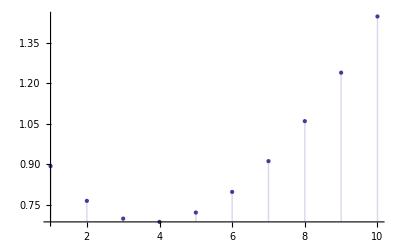

{0.0346478,0.0945982,0.212717,0.419295,0.752256,1.25762,1.98999,3.01298,4.39965}

```mathematica
DiscretePlot[Log[eucpower[8,m]], {m,1,10}]
Table[N[eucpower[n,4]],{n,2,10}]
```

## The probability of error

```mathematica
Pe[n_,v_,t_] :=1 - Sum[(-1)^m/2^m/v^m/Factorial[m]*eucpower[n,m],{m,0,t}]/(2*Pi*v)^(n/2);
N[Pe[2,10/100,33]]
```

0.0652598

```mathematica
approx = Import["Software/pubtex/quantisingandcodingwithAn/plots/n8approxpc","Table"]
```

{{1.,0.999001},{0.933333,0.999001},{0.871111,0.998004},{0.813037,0.999001},{0.758835,0.995025},{0.708246,0.995025},{0.661029,0.997009},{0.616961,0.994036},{0.57583,0.993049},{0.537441,0.992063},{0.501612,0.984252},{0.468171,0.982318},{0.43696,0.982318},{0.407829,0.980392},{0.38064,0.970874},{0.355264,0.962464},{0.33158,0.960615},{0.309475,0.932836},{0.288843,0.928505},{0.269587,0.908265},{0.251614,0.899281},{0.23484,0.887311},{0.219184,0.874891},{0.204572,0.848896},{0.190934,0.798085},{0.178205,0.761035},{0.166324,0.740192},{0.155236,0.68918},{0.144887,0.621118},{0.135228,0.606796},{0.126213,0.555556},{0.117799,0.494315},{0.109945,0.438789},{0.102616,0.411862},{0.0957746,0.359583},{0.0893896,0.318167},{0.0834303,0.258264},{0.0778683,0.21004},{0.0726771,0.169779},{0.0678319,0.144342},{0.0633098,0.109757},{0.0590892,0.0825355},{0.0551499,0.0701705},{0.0514732,0.0452366},{0.0480417,0.0334381},{0.0448389,0.0221616},{0.0418496,0.0162668},{0.0390597,0.0104194},{0.0364557,0.00659187},{0.0340253,0.00400842},{0.031757,0.00222172},{0.0296398,0.00132006},{0.0276638,0.000730598},{0.0258196,0.000370045},{0.0240983,0.000187555},{0.0224917,0.0000861131},{0.0209923,0.0000383389},{0.0195928,0.0000156332},{0.0182866,6.20597×10^-6},{0.0170675,2.24865×10^-6},{0.0159297,8.06314×10^-7}}

## Plotting the probability of error versus SNR

```mathematica
n = 3;
V = Sqrt[n+1];
vars = Table[1/2*(93/100)^k, {k,0,55}]
snrdb = V^(2/n)/(4#) &/@ vars
pes = Pe[n,1/2*(93/100)^#,281]&/@ vars
ListLogLogPlot[{ vars },Joined->{True}]
```

$Aborted

ListLogLogPlot::argx: ListLogLogPlot called with 0 arguments; 1 argument is expected.

ListLogLogPlot[{{}},Joined→{True}]